```mathematica
MyFolderX=NotebookDirectory[]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/

```mathematica
(* Store filepath (string) of PersonData_ALL_N_354842_ALL.txt file in FilePathX *)
FilePathX=StringJoin[MyFolderX,"PersonData_ALL_N_354842_ALL.txt"]
```

/Users/shawnliang/Desktop/Data & Code/Midterm/PersonData_ALL_N_354842_ALL.txt

```mathematica
(* Import Data > Store in the local variabe "Din" *)
Din=Import[FilePathX,"CSV",CharacterEncoding-> "UTF8","TextDelimiters"->"\""];
```

```mathematica
NDataALL = Length[Din]
```

354842

```mathematica
1.Time Period Between 1890s and 1900s  --Occupation Types in the United States [ ~20 Years before World War II ]
```

```mathematica
HeaderX={"Name","FullName","Gender","NationalityCountries","BirthDate","DeathDate","BirthPlace","DeathPlace","Occupation","Wives","Husbands"};

(* Choose from Dataset to obtain 1890s-1900s indivduals, and cleaning the data by getting rid of NotAvailable data, and rounding the year to decades.*)
```

```mathematica
DinFirst = Reap[For[i = 1,i<=NDataALL, i++,
If[(ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 == 1890 || (ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 ==1900)) &&
(Din[[i]][[4]]== "UnitedStates")&&
(Din[[i]][[3]]== "Male")&&
(Din[[i]][[-3]]!= "NotAvailable")
, Sow[Din[[i]]]
]]][[2]][[1]];
DinFirst[[1;;3]]
Length[DinFirst]
```

{{A. Arnold Gillespie,A. Arnold Gillespie,Male,UnitedStates,1899-10-14,1978-05-03,ElPaso;Texas;UnitedStates,LosAngeles;California;UnitedStates,academy award winner,Nell_Hill;Dora_Ingram,NotAvailable},{A. B. Guthrie,A. B. Guthrie,Male,UnitedStates,1901-01-13,1991-04-26,Bedford;Indiana;UnitedStates,Choteau;Montana;UnitedStates,novelist,NotAvailable,NotAvailable},{A. Earl Hedrick,NotAvailable,Male,UnitedStates,1896-03-02,1985-09-18,LosAngeles;California;UnitedStates,Whittier;California;UnitedStates,art director,NotAvailable,NotAvailable}}

7472

```mathematica
DinSecond = Reap[For[i = 1, i<NDataALL, i++,
If[(ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 == 1930 || (ToExpression[StringDrop[Din[[i]][[5]],-7]]*10 ==1940)) &&
(Din[[i]][[4]]== "UnitedStates")&&
(Din[[i]][[-3]]!= "NotAvailable"), Sow[Din[[i]]]
]]][[2]][[1]];
DinSecond[[1;;3]]
Length[DinSecond]
```

{{A. C. Cowlings,Allen G. Cowlings,Male,UnitedStates,1947-06-16,NotAvailable,SanFrancisco;California;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},{A.D. Whitfield,A.D. Whitfield,Male,UnitedStates,1943-09-02,NotAvailable,Rosebud;Texas;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable},{A.D. Williams,A.D. Williams,Male,UnitedStates,1933-11-21,NotAvailable,LittleRock;Arkansas;UnitedStates,NotAvailable,football player,NotAvailable,NotAvailable}}

19327

```mathematica
2. Count Different Birth Years and Occupation Types from People Dataset
```

```mathematica
DBirthYearFirst = DinFirst
DBirthYearFirst= Reap[For[i = 1, i <= Length[DBirthYearFirst], i++,
Sow[ToExpression[StringDrop[DBirthYearFirst[[i]][[5]],-7]]*10]]][[2]][[1]];
```

{{A. Arnold Gillespie,A. Arnold Gillespie,Male,UnitedStates,1899-10-14,1978-05-03,ElPaso;Texas;UnitedStates,LosAngeles;California;UnitedStates,academy award winner,Nell_Hill;Dora_Ingram,NotAvailable},7470,{Fielding L. Wright,Fielding Lewis Wright,Male,UnitedStates,1895-05-16,1956-05-04,RollingFork;Mississippi;UnitedStates,Jackson;Mississippi;UnitedStates,politician,Nan Kelly,NotAvailable}}
 |  |  |  |

```mathematica
(*The Amount of in this dataset *)
Length[DBirthYearFirst]
DBirthYearFirst[[1;;10]]
```

7472

{1890,1900,1890,1890,1900,1900,1890,1900,1900,1900}

```mathematica
DOccupationsFirst= DinFirst
DOccupationsFirst= Reap[For[i = 1, i <= Length[DOccupationsFirst], i++,
Sow[DOccupationsFirst[[i]][[-3]]]]][[2]][[1]];
```

{{A. Arnold Gillespie,A. Arnold Gillespie,Male,UnitedStates,1899-10-14,1978-05-03,ElPaso;Texas;UnitedStates,LosAngeles;California;UnitedStates,academy award winner,Nell_Hill;Dora_Ingram,NotAvailable},7470,{Fielding L. Wright,Fielding Lewis Wright,Male,UnitedStates,1895-05-16,1956-05-04,RollingFork;Mississippi;UnitedStates,Jackson;Mississippi;UnitedStates,politician,Nan Kelly,NotAvailable}}
 |  |  |  |

```mathematica
(* Combine Year and Occupation data sets,
sepereate the occupations for when an indidual has more than one *)
```

```mathematica
DOC = Transpose[{DBirthYearFirst,DOccupationsFirst}];
DOC[[1;;2]]

SplitDOC = Reap[For[i = 1,i≤Length[DOC],i++,
s = StringSplit[DOC[[i,2]],";"];

For[j = 1,j≤ Length[s],j++,
Sow[{DOC[[i,1]],s[[j]]}]
]

]][[2]][[1]];
```

{{1890,academy award winner},{1900,novelist}}

```mathematica
(* Tally the data and get the repeated times in dataset for years and occupations)
```

```mathematica
YDOC = Tally[Flatten[SplitDOC[[All,1]]]];
TableForm[YDOC]
ODOC=Tally[Flatten[SplitDOC[[All,2]]]];
TableForm[ODOC]
```

1890 | 3933
1900 | 4809

academy award winner | 115
novelist | 69
art director | 54
film director | 164
journalist | 65
businessperson | 114
president | 11
screenwriter | 114
military | 175
artist | 58
composer | 71
officer | 70
baseball player | 2539
economist | 19
bandleader | 22
football player | 944
criminal | 29
athlete | 322
actor | 496
mathematician | 53
politician | 295
judge | 272
psychologist | 25
cinematographer | 14
historian | 63
author | 153
musician | 148
sculptor | 4
aviator | 20
inventor | 50
naturalist | 6
writer | 204
singer | 46
priest | 2
basketball coach | 6
lawyer | 75
sinologist | 1
university teacher | 3
scientist | 31
representative | 20
editor | 18
cartoonist | 11
academy award nominee | 177
lyricist | 14
comedian | 16
pianist | 26
test pilot | 1
dentist | 2
clarinetist | 1
botanist | 7
playwright | 37
philanthropist | 14
entrepreneur | 8
organist | 2
educator | 38
jockey | 12
attorney | 26
producer | 35
songwriter | 51
guitarist | 20
soldier | 4
microbiologist | 1
professor | 38
essayist | 4
academic | 9
poet | 42
radiologist | 2
film producer | 52
banker | 9
diplomat | 50
music producer | 3
conductor | 9
arranger | 12
biologist | 9
performer | 8
vocalist | 9
painter | 37
astronomer | 12
photographer | 19
teacher | 12
racehorse owner | 2
racehorse breeder | 1
animator | 7
voice actor | 2
director | 22
football coach | 25
environmental scientist | 1
surgeon | 7
humanitarian | 1
captain | 4
physiologist | 4
government | 65
basketball player | 17
accountant | 2
jazz pianist | 1
physicist | 32
publisher | 18
dancer | 8
civil servant | 4
runner | 5
computer programmer | 4
columnist | 5
critic | 18
ufologist | 1
engineer | 36
manufacturer | 4
anthropologist | 20
administrator | 12
scholar | 10
designer | 7
doctor | 4
production designer | 9
crystallographer | 2
auto racer | 18
fan | 1
tennis player | 1
activist | 14
record producer | 13
radio personality | 4
broadcaster | 3
submariner | 4
linguist | 9
architect | 27
solicitor | 1
photojournalist | 2
war photographer | 1
biochemist | 7
chemist | 26
bridge player | 2
seismologist | 1
sociologist | 8
librarian | 2
television editor | 2
film editor | 5
military officer | 1
golfer | 10
promoter | 2
military personnel | 30
american football player | 3
scenographer | 18
jazz musician | 4
art critic | 2
illustrator | 9
psychobiologist | 1
boxing trainer | 1
coach | 1
religious | 15
computer scientist | 1
rum-running | 2
gangster | 6
racketeering | 2
ornithologist | 3
filmmaker | 4
television producer | 8
television director | 8
animal trainer | 5
presenter | 2
aeronautical engineer | 2
agronomist | 1
geneticist | 5
boss | 2
financier | 2
chief technology officer | 1
information theorist | 1
catholic priest | 1
drummer | 6
street artist | 1
singer-songwriter | 1
zoologist | 6
geologist | 2
traveler | 1
royalty | 1
bishop | 4
lexicographer | 1
disc jockey | 2
legislator | 3
mineralogist | 1
geophysicist | 2
professional boxer | 3
comics artist | 1
psychiatrist | 7
immunologist | 1
orchestration | 1
political scientist | 2
neurologist | 1
philosopher | 15
literary critic | 3
logician | 1
federal judge | 2
general officer | 4
engraver | 1
kidnapping | 1
lacrosse player | 2
translator | 6
community organizer | 1
vocal coach | 1
automobile designer | 1
bank robber | 2
rapper | 1
admiral | 1
public servant | 1
mafioso | 4
wrestler | 1
ecologist | 3
spy | 1
choreographer | 1
physician | 9
college president | 1
rabbi | 1
advertising executive | 1
chief executive officer | 2
curator | 1
set decorator | 5
neurosurgeon | 1
nightclub owner | 1
restaurateur | 1
psychotherapist | 1
hypnotherapist | 1
hypnotist | 1
singer/songwriter | 3
archaeologist | 2
cyclist | 1
assassin | 1
sound engineer | 1
ice hockey player | 5
dairy farmer | 1
fisherman | 1
medical researcher | 5
oceanographer | 2
sound mixer | 1
sound editor | 2
welder | 1
theater director | 3
consultant | 2
art collector | 1
paleontologist | 3
sports figure | 1
sportswriter | 1
model | 1
pilot | 4
jeweler | 2
pathologist | 2
virologist | 3
magician | 2
meteorologist | 1
mammalogist | 1
industrial designer | 1
farmer | 7
beekeeper | 1
retired | 1
university professor | 1
saxophonist | 2
veteran | 1
master | 1
boxer | 3
labor leader | 3
theatre critic | 1
civil engineer | 1
immunochemist | 1
head coach | 1
tv personality | 1
film studio executive | 1
environmentalist | 1
missionary | 2
typographer | 2
camera operator | 1
literary agent | 1
hotel manager | 1
forester | 1
vice president | 1
commentator | 2
game designer | 2
violinist | 2
theologian | 1
executive | 1
statistician | 1
chef | 2
merchant | 1
non-fiction writer | 1
bacteriologist | 1
pharmacologist | 1
hairstylist | 1
music historian | 1
peace activist | 1
preacher | 1
talent agent | 1
intellectual | 1
brigadier | 2
commander | 3
trade unionist | 2
biophysicist | 1
salesman | 4
psychophysicist | 1
folklorist | 1
skeleton racer | 1
bobsledder | 1
music critic | 1
landscape architect | 1
public speaker | 1
type designer | 1
government official | 1
audio engineer | 1
vaudeville performer | 1
mountaineer | 1
explorer | 1
epidemiologist | 1
lighting designer | 1
diarist | 1
climatologist | 1
military leader | 1
anarchist | 1
singer-songwriter | 1
weightlifter | 1
strongman | 1
law enforcement officer | 1
roller coaster designer | 1
executioner | 1
metallurgist | 1
stunt performer | 1
drug trafficker | 1
oboist | 1
musical instrument maker | 1

```mathematica
3) Define Bipartite matrix associating people with their interests - use a sorted interest-index
```

```mathematica
(* Only take the first 200 data from the split data, because the larger the dataset, the messier the graphs.
This way we can have a more clear overall analysis.*)
NewDOC = SplitDOC[[1;;200]];
NewDOC[[-1]]
```

{1900,criminal}

```mathematica
NewODOC = Tally[Flatten[NewDOC[[All,2]]]];
TableForm[NewODOC]
Length[NewODOC]
(* Below are the first 200 occupations and number of times they appear in 1890s - 1900s *)
```

academy award winner | 4
novelist | 1
art director | 3
film director | 4
journalist | 1
businessperson | 2
president | 2
screenwriter | 3
military | 3
artist | 4
composer | 2
officer | 2
baseball player | 68
economist | 1
bandleader | 1
football player | 38
criminal | 3
athlete | 6
actor | 12
mathematician | 2
politician | 5
judge | 5
psychologist | 1
cinematographer | 1
historian | 2
author | 3
musician | 1
sculptor | 1
aviator | 1
inventor | 1
naturalist | 1
writer | 1
singer | 1
priest | 1
basketball coach | 1
lawyer | 1
sinologist | 1
university teacher | 1
scientist | 1
representative | 1
editor | 1
cartoonist | 1
academy award nominee | 2
lyricist | 1
comedian | 1
pianist | 1

46

```mathematica
(* Create "dictionary" which maps a person/interest name to an index *)
Clear[MapYeari]
For[i=1,i≤Length[YDOC],i++,MapYeari[YDOC[[i,1]]]=i; ];
```

```mathematica
MapYeari[YDOC[[1,1]]]
MapYeari[YDOC[[-1,1]]]
```

1

2

```mathematica
Clear[MapOccupationj];
For[i=1,i≤Length[NewODOC],i++,MapOccupationj[NewODOC[[i]][[1]]]=i; ];
MapOccupationj["cartoonist"]
```

42

```mathematica
Length[NewODOC]
```

46

```mathematica
(* Calculate the bipartite association matrix *)
YearOccupationMatrix=Array[0&,{Length[YDOC],Length[NewODOC]}];
For[i=1,i≤Length[NewDOC],i++,
nInt=MapOccupationj[NewDOC[[i,2]]];
mInt=MapYeari[NewDOC[[i,1]]];
YearOccupationMatrix[[mInt]][[nInt]]=YearOccupationMatrix[[mInt]][[nInt]]+1;
];

MatrixForm[YearOccupationMatrix]
```

(3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1)

```mathematica
Show[Colorize[YearOccupationMatrix],ImageSize-> 400,AspectRatio-> 1]
```

-Graphics-

```mathematica
4) Define Year-Year and Occupation-Occupation association matrix using bipartite projection method
```

```mathematica
(* Year-Year association matrix *)
YearYearBipartiteProj=YearOccupationMatrix.Transpose[YearOccupationMatrix];
Length[YearYearBipartiteProj]
For[i=1,i≤ Length[YearYearBipartiteProj],i++, YearYearBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)
MatrixForm[YearYearBipartiteProj] (* Number of occupations are the same in these years*)
```

2

(0 | 1584
1584 | 0)

```mathematica
(* Occupation-Occupation association matrix *)
OccupationOccupationBipartiteProj=Transpose[YearOccupationMatrix].YearOccupationMatrix;
Length[OccupationOccupationBipartiteProj]
For[i=1,i≤ Length[OccupationOccupationBipartiteProj],i++, OccupationOccupationBipartiteProj[[i]][[i]]=0;] 
(* Delete diagonal elements *)

(* Display Matrix of first 20 occupaton to occupation *)
MatrixForm[OccupationOccupationBipartiteProj]
```

46

(0 | 1 | 5 | 10 | 1 | 4 | 4 | 5 | 3 | 8 | 4 | 4 | 134 | 1 | 3 | 78 | 5 | 10 | 24 | 2 | 5 | 7 | 1 | 1 | 4 | 9 | 1 | 3 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 1 | 1 | 3 | 3 | 3 | 1 | 2 | 1 | 1 | 1
1 | 0 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
5 | 2 | 0 | 5 | 2 | 3 | 3 | 5 | 6 | 6 | 3 | 3 | 103 | 2 | 1 | 56 | 5 | 10 | 18 | 4 | 10 | 9 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 4 | 2 | 2 | 2
10 | 1 | 5 | 0 | 1 | 4 | 4 | 5 | 3 | 8 | 4 | 4 | 134 | 1 | 3 | 78 | 5 | 10 | 24 | 2 | 5 | 7 | 1 | 1 | 4 | 9 | 1 | 3 | 3 | 3 | 1 | 1 | 3 | 3 | 1 | 1 | 1 | 1 | 3 | 3 | 3 | 1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 0 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
4 | 1 | 3 | 4 | 1 | 0 | 2 | 3 | 3 | 4 | 2 | 2 | 68 | 1 | 1 | 38 | 3 | 6 | 12 | 2 | 5 | 5 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1
4 | 1 | 3 | 4 | 1 | 2 | 0 | 3 | 3 | 4 | 2 | 2 | 68 | 1 | 1 | 38 | 3 | 6 | 12 | 2 | 5 | 5 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1
5 | 2 | 5 | 5 | 2 | 3 | 3 | 0 | 6 | 6 | 3 | 3 | 103 | 2 | 1 | 56 | 5 | 10 | 18 | 4 | 10 | 9 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 4 | 2 | 2 | 2
3 | 3 | 6 | 3 | 3 | 3 | 3 | 6 | 0 | 6 | 3 | 3 | 105 | 3 | 0 | 54 | 6 | 12 | 18 | 6 | 15 | 12 | 3 | 3 | 3 | 0 | 3 | 0 | 0 | 0 | 3 | 3 | 0 | 0 | 3 | 3 | 3 | 3 | 0 | 0 | 0 | 3 | 6 | 3 | 3 | 3
8 | 2 | 6 | 8 | 2 | 4 | 4 | 6 | 6 | 0 | 4 | 4 | 136 | 2 | 2 | 76 | 6 | 12 | 24 | 4 | 10 | 10 | 2 | 2 | 4 | 6 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 2 | 4 | 2 | 2 | 2
4 | 1 | 3 | 4 | 1 | 2 | 2 | 3 | 3 | 4 | 0 | 2 | 68 | 1 | 1 | 38 | 3 | 6 | 12 | 2 | 5 | 5 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1
4 | 1 | 3 | 4 | 1 | 2 | 2 | 3 | 3 | 4 | 2 | 0 | 68 | 1 | 1 | 38 | 3 | 6 | 12 | 2 | 5 | 5 | 1 | 1 | 2 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1
134 | 35 | 103 | 134 | 35 | 68 | 68 | 103 | 105 | 136 | 68 | 68 | 0 | 35 | 33 | 1290 | 103 | 206 | 408 | 70 | 175 | 173 | 35 | 35 | 68 | 99 | 35 | 33 | 33 | 33 | 35 | 35 | 33 | 33 | 35 | 35 | 35 | 35 | 33 | 33 | 33 | 35 | 70 | 35 | 35 | 35
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 0 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 0 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
78 | 18 | 56 | 78 | 18 | 38 | 38 | 56 | 54 | 76 | 38 | 38 | 1290 | 18 | 20 | 0 | 56 | 112 | 228 | 36 | 90 | 92 | 18 | 18 | 38 | 60 | 18 | 20 | 20 | 20 | 18 | 18 | 20 | 20 | 18 | 18 | 18 | 18 | 20 | 20 | 20 | 18 | 36 | 18 | 18 | 18
5 | 2 | 5 | 5 | 2 | 3 | 3 | 5 | 6 | 6 | 3 | 3 | 103 | 2 | 1 | 56 | 0 | 10 | 18 | 4 | 10 | 9 | 2 | 2 | 3 | 3 | 2 | 1 | 1 | 1 | 2 | 2 | 1 | 1 | 2 | 2 | 2 | 2 | 1 | 1 | 1 | 2 | 4 | 2 | 2 | 2
10 | 4 | 10 | 10 | 4 | 6 | 6 | 10 | 12 | 12 | 6 | 6 | 206 | 4 | 2 | 112 | 10 | 0 | 36 | 8 | 20 | 18 | 4 | 4 | 6 | 6 | 4 | 2 | 2 | 2 | 4 | 4 | 2 | 2 | 4 | 4 | 4 | 4 | 2 | 2 | 2 | 4 | 8 | 4 | 4 | 4
24 | 6 | 18 | 24 | 6 | 12 | 12 | 18 | 18 | 24 | 12 | 12 | 408 | 6 | 6 | 228 | 18 | 36 | 0 | 12 | 30 | 30 | 6 | 6 | 12 | 18 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 6 | 12 | 6 | 6 | 6
2 | 2 | 4 | 2 | 2 | 2 | 2 | 4 | 6 | 4 | 2 | 2 | 70 | 2 | 0 | 36 | 4 | 8 | 12 | 0 | 10 | 8 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 4 | 2 | 2 | 2
5 | 5 | 10 | 5 | 5 | 5 | 5 | 10 | 15 | 10 | 5 | 5 | 175 | 5 | 0 | 90 | 10 | 20 | 30 | 10 | 0 | 20 | 5 | 5 | 5 | 0 | 5 | 0 | 0 | 0 | 5 | 5 | 0 | 0 | 5 | 5 | 5 | 5 | 0 | 0 | 0 | 5 | 10 | 5 | 5 | 5
7 | 4 | 9 | 7 | 4 | 5 | 5 | 9 | 12 | 10 | 5 | 5 | 173 | 4 | 1 | 92 | 9 | 18 | 30 | 8 | 20 | 0 | 4 | 4 | 5 | 3 | 4 | 1 | 1 | 1 | 4 | 4 | 1 | 1 | 4 | 4 | 4 | 4 | 1 | 1 | 1 | 4 | 8 | 4 | 4 | 4
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
4 | 1 | 3 | 4 | 1 | 2 | 2 | 3 | 3 | 4 | 2 | 2 | 68 | 1 | 1 | 38 | 3 | 6 | 12 | 2 | 5 | 5 | 1 | 1 | 0 | 3 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 2 | 1 | 1 | 1
9 | 0 | 3 | 9 | 0 | 3 | 3 | 3 | 0 | 6 | 3 | 3 | 99 | 0 | 3 | 60 | 3 | 6 | 18 | 0 | 0 | 3 | 0 | 0 | 3 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 3 | 3 | 0 | 0 | 0 | 0 | 3 | 3 | 3 | 0 | 0 | 0 | 0 | 0
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 1
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 0 | 0 | 0
3 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 2 | 1 | 1 | 33 | 0 | 1 | 20 | 1 | 2 | 6 | 0 | 0 | 1 | 0 | 0 | 1 | 3 | 0 | 1 | 1 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 2 | 1 | 1 | 1
2 | 2 | 4 | 2 | 2 | 2 | 2 | 4 | 6 | 4 | 2 | 2 | 70 | 2 | 0 | 36 | 4 | 8 | 12 | 4 | 10 | 8 | 2 | 2 | 2 | 0 | 2 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 2 | 2 | 2 | 2 | 0 | 0 | 0 | 2 | 0 | 2 | 2 | 2
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 0 | 1 | 1
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 0 | 1
1 | 1 | 2 | 1 | 1 | 1 | 1 | 2 | 3 | 2 | 1 | 1 | 35 | 1 | 0 | 18 | 2 | 4 | 6 | 2 | 5 | 4 | 1 | 1 | 1 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 1 | 1 | 1 | 0 | 0 | 0 | 1 | 2 | 1 | 1 | 0)

```mathematica
(* Degree Distribution *)
DegreeX=Total[Sign[#]]&/@OccupationOccupationBipartiteProj
```

{45,35,45,45,35,45,45,45,35,45,45,45,45,35,25,45,45,45,45,35,35,45,35,35,45,25,35,25,25,25,35,35,25,25,35,35,35,35,25,25,25,35,35,35,35,35}

```mathematica
5) WeightedAdjacencyGraph[ ]
```

```mathematica
mat=Replace[OccupationOccupationBipartiteProj,0->Infinity,{2}]; (*  0s represented by infinity in WeightedAdjacencyGraph[ ] *)
OName=NewODOC[[All,1]];

(* Set Labels : The "keys" for each node will be the name stored in OName *)
NameFontSizeX=20;
NodeColorX=Black;
LabelsetBlack=Table[OName[[i]]->Placed[ Style[OName[[i]],FontFamily->"Helvetica",NameFontSizeX,NodeColorX],Center],{i,Length[OName]}]
```

{academy award winner→Placed[academy award winner,Center],novelist→Placed[novelist,Center],art director→Placed[art director,Center],film director→Placed[film director,Center],politician→Placed[politician,Center],journalist→Placed[journalist,Center],head teacher→Placed[head teacher,Center],city attorney→Placed[city attorney,Center],lawyer→Placed[lawyer,Center],superintendent→Placed[superintendent,Center],teacher→Placed[teacher,Center],businessperson→Placed[businessperson,Center],president→Placed[president,Center],screenwriter→Placed[screenwriter,Center],administrator→Placed[administrator,Center],diplomat→Placed[diplomat,Center],consultant→Placed[consultant,Center],reporter→Placed[reporter,Center],board of directors→Placed[board of directors,Center],military→Placed[military,Center],artist→Placed[artist,Center],composer→Placed[composer,Center],painter→Placed[painter,Center],officer→Placed[officer,Center],university teacher→Placed[university teacher,Center],photographer→Placed[photographer,Center],baseball player→Placed[baseball player,Center],economist→Placed[economist,Center],lecturer→Placed[lecturer,Center],bandleader→Placed[bandleader,Center],football player→Placed[football player,Center],criminal→Placed[criminal,Center],athlete→Placed[athlete,Center],actor→Placed[actor,Center],mathematician→Placed[mathematician,Center],judge→Placed[judge,Center],psychologist→Placed[psychologist,Center],cinematographer→Placed[cinematographer,Center],historian→Placed[historian,Center],author→Placed[author,Center],musician→Placed[musician,Center],sculptor→Placed[sculptor,Center],aviator→Placed[aviator,Center],inventor→Placed[inventor,Center],naturalist→Placed[naturalist,Center],writer→Placed[writer,Center],textile designer→Placed[textile designer,Center],industrial designer→Placed[industrial designer,Center],architect→Placed[architect,Center],singer→Placed[singer,Center],performer→Placed[performer,Center],dancer→Placed[dancer,Center],priest→Placed[priest,Center],basketball coach→Placed[basketball coach,Center],fashion designer→Placed[fashion designer,Center],sinologist→Placed[sinologist,Center],scientist→Placed[scientist,Center],representative→Placed[representative,Center],critic→Placed[critic,Center],voice actor→Placed[voice actor,Center],editor→Placed[editor,Center],secretary→Placed[secretary,Center],religious→Placed[religious,Center],cartoonist→Placed[cartoonist,Center]}

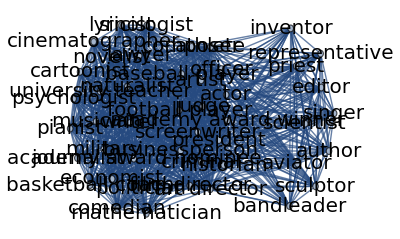

```mathematica
(* Plot Network - an ugly mess *)
g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack]
```

```mathematica
Clustering Coefficients - to what degree are neighbors connected?
```

```mathematica
(* Global - Network-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)
N[GlobalClusteringCoefficient[g]]
```

0.895901

```mathematica
(* Local - Node-level characteristic: What fraction of possible triangles (1st order cycle) exist in the network *)LClusteringCoeffX=N[LocalClusteringCoefficient[g]]
Mean[LClusteringCoeffX]
N[MeanClusteringCoefficient[g]] (* Gives same result as above *)
```

{0.79798,1.,0.79798,0.79798,1.,0.79798,0.79798,0.79798,1.,0.79798,0.79798,0.79798,0.79798,1.,1.,0.79798,0.79798,0.79798,0.79798,1.,1.,0.79798,1.,1.,0.79798,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.,1.}

0.929732

0.929732

```mathematica
Length[LClusteringCoeffX]
```

46

```mathematica
Length[OName]
```

64

```mathematica
Sort[Thread[Rule[OName,LClusteringCoeffX]],#1[[2]]>#2[[2]]&]
```

{pianist→1.,comedian→1.,lyricist→1.,academy award nominee→1.,cartoonist→1.,editor→1.,representative→1.,scientist→1.,university teacher→1.,sinologist→1.,lawyer→1.,basketball coach→1.,priest→1.,singer→1.,writer→1.,naturalist→1.,inventor→1.,aviator→1.,sculptor→1.,musician→1.,author→1.,cinematographer→1.,psychologist→1.,politician→1.,mathematician→1.,bandleader→1.,economist→1.,military→1.,journalist→1.,novelist→1.,historian→0.79798,judge→0.79798,actor→0.79798,athlete→0.79798,criminal→0.79798,football player→0.79798,baseball player→0.79798,officer→0.79798,composer→0.79798,artist→0.79798,screenwriter→0.79798,president→0.79798,businessperson→0.79798,film director→0.79798,art director→0.79798,academy award winner→0.79798}

{{45,0.79798},{35,1.},{45,0.79798},{45,0.79798},{35,1.},{45,0.79798},{45,0.79798},{45,0.79798},{35,1.},{45,0.79798},{45,0.79798},{45,0.79798},{45,0.79798},{35,1.},{25,1.},{45,0.79798},{45,0.79798},{45,0.79798},{45,0.79798},{35,1.},{35,1.},{45,0.79798},{35,1.},{35,1.},{45,0.79798},{25,1.},{35,1.},{25,1.},{25,1.},{25,1.},{35,1.},{35,1.},{25,1.},{25,1.},{35,1.},{35,1.},{35,1.},{35,1.},{25,1.},{25,1.},{25,1.},{35,1.},{35,1.},{35,1.},{35,1.},{35,1.}}

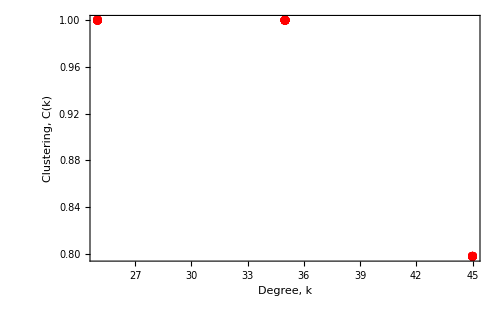

```mathematica
DegreeClusteringX=Thread[{DegreeX,LClusteringCoeffX}]

ListPlot[DegreeClusteringX,
PlotRange-> All,
PlotStyle->Directive[Red,10],
LabelStyle -> Directive[Black,FontSize->20,FontFamily-> "Helvetica"],
Frame->True,
ImageSize->{500,Automatic},
FrameLabel->{"Degree, k","Clustering, C(k)"},
ImageSize->500]
```

```mathematica
Improve network visualization layout
```

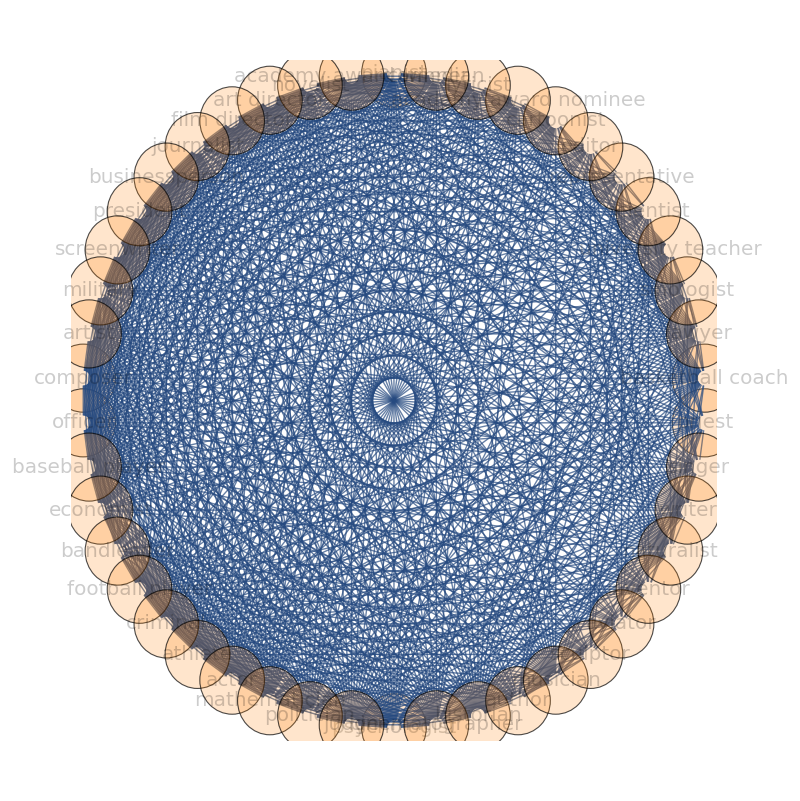

```mathematica
Circlesize=0.05;
r=Array[Circlesize&,Length[OName]]; (* Circle radius list *)

g=WeightedAdjacencyGraph[OName,mat,VertexLabels->LabelsetBlack,VertexSize->Scaled[.10],VertexStyle->Directive[Orange,Opacity[.2]],GraphLayout->{"CircularEmbedding"} ,ImageSize->800]
```

```mathematica
6) Modify the link color and thickness
```

```mathematica
(* AbsoluteOptions[ ]: gives the absolute settings of options specified in an expression such as a graphics object. *)
gEdWe=AbsoluteOptions[g,EdgeWeight][[All,2]][[1]]  (* Get list of edge weights associated with each edge *)
Max[gEdWe]
```

{1,5,10,1,4,4,5,3,8,4,4,134,1,3,78,5,10,24,2,5,7,1,1,4,9,1,3,3,3,1,1,3,3,1,1,1,1,3,3,3,1,2,1,1,1,2,1,1,1,1,2,3,2,1,1,35,1,18,2,4,6,2,5,4,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,5,2,3,3,5,6,6,3,3,103,2,1,56,5,10,18,4,10,9,2,2,3,3,2,1,1,1,2,2,1,1,2,2,2,2,1,1,1,2,4,2,2,2,1,4,4,5,3,8,4,4,134,1,3,78,5,10,24,2,5,7,1,1,4,9,1,3,3,3,1,1,3,3,1,1,1,1,3,3,3,1,2,1,1,1,1,1,2,3,2,1,1,35,1,18,2,4,6,2,5,4,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,2,3,3,4,2,2,68,1,1,38,3,6,12,2,5,5,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,3,4,2,2,68,1,1,38,3,6,12,2,5,5,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,6,6,3,3,103,2,1,56,5,10,18,4,10,9,2,2,3,3,2,1,1,1,2,2,1,1,2,2,2,2,1,1,1,2,4,2,2,2,6,3,3,105,3,54,6,12,18,6,15,12,3,3,3,3,3,3,3,3,3,3,3,6,3,3,3,4,4,136,2,2,76,6,12,24,4,10,10,2,2,4,6,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,2,68,1,1,38,3,6,12,2,5,5,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,68,1,1,38,3,6,12,2,5,5,1,1,2,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,35,33,1290,103,206,408,70,175,173,35,35,68,99,35,33,33,33,35,35,33,33,35,35,35,35,33,33,33,35,70,35,35,35,18,2,4,6,2,5,4,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,20,1,2,6,1,1,3,1,1,1,1,1,1,1,1,56,112,228,36,90,92,18,18,38,60,18,20,20,20,18,18,20,20,18,18,18,18,20,20,20,18,36,18,18,18,10,18,4,10,9,2,2,3,3,2,1,1,1,2,2,1,1,2,2,2,2,1,1,1,2,4,2,2,2,36,8,20,18,4,4,6,6,4,2,2,2,4,4,2,2,4,4,4,4,2,2,2,4,8,4,4,4,12,30,30,6,6,12,18,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,6,12,6,6,6,10,8,2,2,2,2,2,2,2,2,2,2,2,4,2,2,2,20,5,5,5,5,5,5,5,5,5,5,5,10,5,5,5,4,4,5,3,4,1,1,1,4,4,1,1,4,4,4,4,1,1,1,4,8,4,4,4,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,3,3,3,3,3,3,3,3,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,1,1,2,1,1,1,1,2,1,1,1,1,1,1,2,1,1,1,2,2,2,1,1,1}

1290

```mathematica
(* Use linear transform to rescale edge weight values to be from 0 to 1 *)
gEdWe=Rescale[gEdWe,{0,Max[gEdWe]},{0,1}]
```

{1/1290,1/258,1/129,1/1290,2/645,2/645,1/258,1/430,4/645,2/645,2/645,67/645,1/1290,1/430,13/215,1/258,1/129,4/215,1/645,1/258,7/1290,1/1290,1/1290,2/645,3/430,1/1290,1/430,1/430,1/430,1/1290,1/1290,1/430,1/430,1/1290,1/1290,1/1290,1/1290,1/430,1/430,1/430,1/1290,1/645,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/645,1/430,1/645,1/1290,1/1290,7/258,1/1290,3/215,1/645,2/645,1/215,1/645,1/258,2/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/258,1/645,1/430,1/430,1/258,1/215,1/215,1/430,1/430,103/1290,1/645,1/1290,28/645,1/258,1/129,3/215,2/645,1/129,3/430,1/645,1/645,1/430,1/430,1/645,1/1290,1/1290,1/1290,1/645,1/645,1/1290,1/1290,1/645,1/645,1/645,1/645,1/1290,1/1290,1/1290,1/645,2/645,1/645,1/645,1/645,1/1290,2/645,2/645,1/258,1/430,4/645,2/645,2/645,67/645,1/1290,1/430,13/215,1/258,1/129,4/215,1/645,1/258,7/1290,1/1290,1/1290,2/645,3/430,1/1290,1/430,1/430,1/430,1/1290,1/1290,1/430,1/430,1/1290,1/1290,1/1290,1/1290,1/430,1/430,1/430,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/430,1/645,1/1290,1/1290,7/258,1/1290,3/215,1/645,2/645,1/215,1/645,1/258,2/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/645,1/430,1/430,2/645,1/645,1/645,34/645,1/1290,1/1290,19/645,1/430,1/215,2/215,1/645,1/258,1/258,1/1290,1/1290,1/645,1/430,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/430,1/430,2/645,1/645,1/645,34/645,1/1290,1/1290,19/645,1/430,1/215,2/215,1/645,1/258,1/258,1/1290,1/1290,1/645,1/430,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/215,1/215,1/430,1/430,103/1290,1/645,1/1290,28/645,1/258,1/129,3/215,2/645,1/129,3/430,1/645,1/645,1/430,1/430,1/645,1/1290,1/1290,1/1290,1/645,1/645,1/1290,1/1290,1/645,1/645,1/645,1/645,1/1290,1/1290,1/1290,1/645,2/645,1/645,1/645,1/645,1/215,1/430,1/430,7/86,1/430,9/215,1/215,2/215,3/215,1/215,1/86,2/215,1/430,1/430,1/430,1/430,1/430,1/430,1/430,1/430,1/430,1/430,1/430,1/215,1/430,1/430,1/430,2/645,2/645,68/645,1/645,1/645,38/645,1/215,2/215,4/215,2/645,1/129,1/129,1/645,1/645,2/645,1/215,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,2/645,1/645,1/645,1/645,1/645,34/645,1/1290,1/1290,19/645,1/430,1/215,2/215,1/645,1/258,1/258,1/1290,1/1290,1/645,1/430,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,34/645,1/1290,1/1290,19/645,1/430,1/215,2/215,1/645,1/258,1/258,1/1290,1/1290,1/645,1/430,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,7/258,11/430,1,103/1290,103/645,68/215,7/129,35/258,173/1290,7/258,7/258,34/645,33/430,7/258,11/430,11/430,11/430,7/258,7/258,11/430,11/430,7/258,7/258,7/258,7/258,11/430,11/430,11/430,7/258,7/129,7/258,7/258,7/258,3/215,1/645,2/645,1/215,1/645,1/258,2/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,2/129,1/1290,1/645,1/215,1/1290,1/1290,1/430,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,28/645,56/645,38/215,6/215,3/43,46/645,3/215,3/215,19/645,2/43,3/215,2/129,2/129,2/129,3/215,3/215,2/129,2/129,3/215,3/215,3/215,3/215,2/129,2/129,2/129,3/215,6/215,3/215,3/215,3/215,1/129,3/215,2/645,1/129,3/430,1/645,1/645,1/430,1/430,1/645,1/1290,1/1290,1/1290,1/645,1/645,1/1290,1/1290,1/645,1/645,1/645,1/645,1/1290,1/1290,1/1290,1/645,2/645,1/645,1/645,1/645,6/215,4/645,2/129,3/215,2/645,2/645,1/215,1/215,2/645,1/645,1/645,1/645,2/645,2/645,1/645,1/645,2/645,2/645,2/645,2/645,1/645,1/645,1/645,2/645,4/645,2/645,2/645,2/645,2/215,1/43,1/43,1/215,1/215,2/215,3/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,1/215,2/215,1/215,1/215,1/215,1/129,4/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,1/645,2/645,1/645,1/645,1/645,2/129,1/258,1/258,1/258,1/258,1/258,1/258,1/258,1/258,1/258,1/258,1/258,1/129,1/258,1/258,1/258,2/645,2/645,1/258,1/430,2/645,1/1290,1/1290,1/1290,2/645,2/645,1/1290,1/1290,2/645,2/645,2/645,2/645,1/1290,1/1290,1/1290,2/645,4/645,2/645,2/645,2/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/430,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/430,1/430,1/430,1/430,1/430,1/430,1/430,1/430,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/1290,1/1290,1/1290,1/645,1/1290,1/1290,1/1290,1/645,1/645,1/645,1/1290,1/1290,1/1290}

```mathematica
(* Adjust the link properties *)
ThicknessBoost=8;
OpacityFactor=1; (* 1.15, 1, 1.1*)
RedGreenFactor=-1; (* 1 = Green, -1 = Red *)

(* Thread together the links with their modified color, opacity, and thickness values defined by gEdWe *)
(* The &/@gEdWe means that everywhere that there is a # in the Thread function it will use the corresponding list element in gEdWe *)
ModifiedEdgePropertiesX=
Thread[Rule[EdgeList[g],Directive[ColorData["RedGreenSplit"][Rescale[#,{-1*RedGreenFactor,1 *RedGreenFactor}]],Opacity[(OpacityFactor*#)],AbsoluteThickness[ThicknessBoost*#]]&/@gEdWe]];
Take[ModifiedEdgePropertiesX,3]
```

{academy award winner<->novelist→Directive[RGBColor[1., 0.9992744248062015, 0.9992744248062015],Opacity[1/1290],AbsoluteThickness[4/645]],academy award winner<->art director→Directive[RGBColor[1., 0.9963721240310077, 0.9963721240310077],Opacity[1/258],AbsoluteThickness[4/129]],academy award winner<->film director→Directive[RGBColor[1., 0.9927442480620154, 0.9927442480620154],Opacity[1/129],AbsoluteThickness[8/129]]}

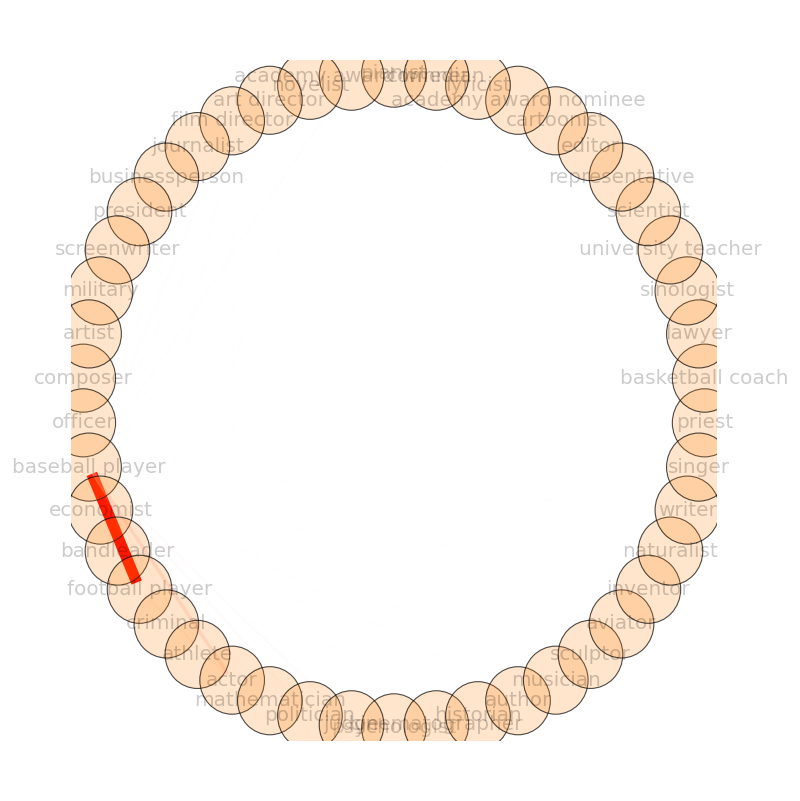

```mathematica
(* Adjust just one option stored in the graph g *)
g=SetProperty[g,EdgeStyle->ModifiedEdgePropertiesX];

Gfin=Show[g,ImagePadding->{{100,100},{100,100}}]
```